```mathematica
(* Matrix elements and cross-sections *)
ClearAll[matrixElement];ClearAll[meA];
matrixElement[eCM_,{N938,D1232},mA_,mB_]:=40000 * (m0[D1232] Γ0[D1232])^2/((eCM^2 -m0[D1232]^2)^2 +( m0[D1232] Γ0[D1232])^2);
matrixElement[eCM_,{D1232,D1232},mA_,mB_]:=2.8;
meA[N938,h_]:=If[MemberQ[Ns,h],6.3,12.0];
meA[D1232,h_]:=3.5;
matrixElement[eCM_,{hA_,hB_},mA_,mB_]:=meA[hA,hB]/((mB-mA)^2(mB+mA)^2);

ClearAll[brFactor];ClearAll[brFactorPts];

brFactorCalc[eCM_,{hC_,hD_}]:=If[eCM≤ minMass[hC]+minMass[hD],0,
(2j[hC]+1)(2j[hD]+1) * pMean[eCM,{hC,hD}] * matrixElement[eCM,{hC,hD},m0[hC],m0[hD]]
];
brFile[{hC_,hD_}]:=brFile[{hC,hD}]=atNotebook["BRs/brFactor_"<>ToString[hC]<>ToString[hD]];
brFactorPts[file_]:=(*brFactorPts[{hA,hB}]=*)
Module[{stream,currentValue,readValues},
stream=OpenRead[file];
readValues=ToExpression/@StringSplit@ReadString[stream];
Close[stream];
Return@Transpose[{Table[x,{x,2.,8.,(8.-2.)/(Length[readValues]-1)}],readValues}];
];
brFactor[eCM_,{hC_,hD_}]:=
Block[{file=brFile[{hC,hD}]},
If[FileExistsQ[file],Interpolation[brFactorPts[file],eCM],brFactorCalc[eCM,{hC,hD}]]
];

ClearAll[σDiffractiveNN];
σDiffractiveNN[eCM_,{hC_,hD_}]:=If[eCM≤2m0[N938],0,
(2j[hC]+1)(2j[hD]+1) * pMean[eCM,{hC,hD}] * matrixElement[eCM,{hC,hD},m0[hC],m0[hD]]/(pMean[eCM,{N938,N938}]eCM^2)
];
σDiffractiveNN[eCM_]:=
Monitor[
σDiffractiveNN[eCM,{N938,D1232}]+σDiffractiveNN[eCM,{D1232,D1232}]
+Sum[σDiffractiveNN[eCM,{N938,h}]+σDiffractiveNN[eCM,{D1232,h}],{h,Join[Ns,Ds]}],
h]
```

```mathematica
brFactor[4.,{N938,D1600}]
```

0.488646

```mathematica
Plot[σDiffractiveNN[eCM,{N938,D1600}],{eCM,2.,6.},PlotRange->All]
```

$Aborted

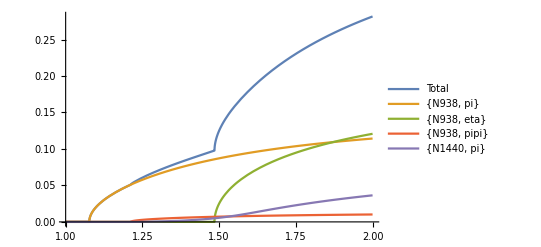

```mathematica
Block[{h=N1535},
Plot[Evaluate@Flatten@{Γ[h,m],Table[Γ[h,hs,m],{hs,decayProducts@h}]},{m,1.,2.},PlotLegends->Flatten@{"Total",ToString/@decayProducts[h]}]
]
```

```mathematica
pMean[3.0,{N938,D1232}]
```

0.796906

```mathematica
massDecayBound@D1232
```

1.077

```mathematica
Γ0@N938
```

0.

```mathematica
Γ0@D1232
```

0.115

```mathematica
2m0@D1232
```

2.464

```mathematica
pMean[2.5,{D1232,D1232}]
```

{1.077,2.5}{1.077,1.423}

0.188874

```mathematica
m0@N938+m0@D1232
```

2.17

```mathematica
pMean[2.5,{N938,D1232}]
```

0.679627

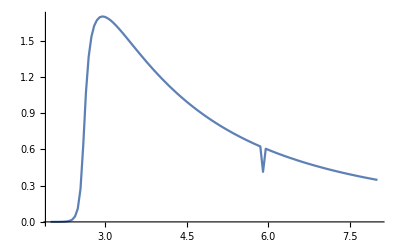

```mathematica
pts= Monitor[
Table[{eCM,sigmapp[eCM,{N938,D1600}]},{eCM,2.0,8.0,0.05}],
ProgressIndicator[eCM,{2.,8.}]
];
ListLinePlot[pts,PlotRange->All]
```

```mathematica
σNNlow=1.8964808;σNNhigh=2.8964808;
σppTable=Transpose[{Table[1.8964808+0.01(n-1),{n,1,100}],{ 39.48,31.76,26.26,24.05,23.94,23.77,23.72,23.98,24.48,24.52,28.72,33.21,37.33,39.87,42.14,44.15,46.85,48.56,48.65,48.97,48.81,48.43,48.36,48.19,47.89,47.53,47.42,47.37,47.17,46.65,46.48,45.94,45.63,45.75,45.52,45.24,45.13,44.96,44.55,44.44,44.10,43.89,43.77,43.32,43.30,43.07,42.95,42.74,42.46,42.28,42.11,41.96,41.86,41.74,41.64,41.54,41.44,41.37,41.29,41.22,41.14,41.09,41.01,40.93,40.83,40.74,40.66,40.58,40.51,40.47,40.40,40.35,40.47,40.44,40.38,40.35,40.32,40.27,40.25,40.23,40.19,40.13,40.11,40.09,40.06,40.02,40.00,39.95,39.94,39.90,39.87,39.82,39.77,39.72,39.67,39.59,39.54,39.48,39.41,39.32}
}];
σpnTable=Transpose[{Table[1.8964808+0.01(n-1),{n,1,100}],
{ 248.20,93.38,55.26,44.50,41.33,38.48,37.20,35.98,35.02,34.47,34.37,34.67,35.23,35.97,36.75,37.37,37.77,38.03,38.40,38.83,39.26,39.67,40.06,40.45,40.79,41.06,41.31,41.52,41.70,41.81,41.87,41.98,42.12,42.29,42.55,42.82,43.01,43.12,43.16,43.14,43.06,42.95,42.81,42.67,42.54,42.45,42.38,42.33,42.30,42.29,42.28,42.26,42.24,42.21,42.17,42.14,42.10,42.07,42.06,42.05,42.04,42.03,42.02,42.00,41.97,41.94,41.89,41.84,41.79,41.73,41.67,41.61,41.55,41.49,41.44,41.38,41.34,41.31,41.29,41.28,41.27,41.28,41.30,41.33,41.36,41.40,41.44,41.49,41.50,41.51,41.51,41.51,41.52,41.51,41.51,41.50,41.50,41.49,41.47,41.46}
}];
```

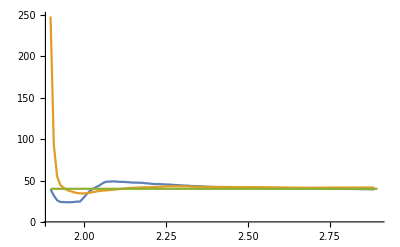

```mathematica
ListLinePlot[{σppTable,σpnTable,Table[{x,40},{x,σNNlow,σNNhigh}]},PlotRange->{0,All}]
```

```mathematica
Length@σppTable
```

100

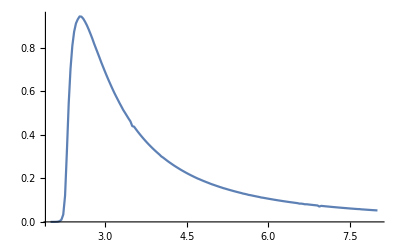

```mathematica
ListLinePlot@brFactorPts[{D1232,D1620}]
```

```mathematica
Length@brFactorPts[{D1232,D1620}]
```

181

```mathematica
(x=4)≠4
```

False